# Environment set up: Need Package PauliAlgebra`

Download url
https://github.com/EverettYou/Mathematica-for-physics

```mathematica
Needs["PauliAlgebra`"]
$PlotTheme="Scientific"
```

Scientific

### Definition of some operator

```mathematica
pauliOp[index_,α_,nsys_]:=(
oplist=Table[0,{i,1,nsys}];
newindex=Mod[index,nsys];
If[newindex==0,newindex=nsys];
oplist[[newindex]]=α;
Return[Apply[σ,oplist]]
)
pauliPlusOp[index_,nsys_]:=(
pauliOp[index,1,nsys]+ⅈ pauliOp[index,2,nsys]);
pauliMinusOp[index_,nsys_]:=(
pauliOp[index,1,nsys]-ⅈ pauliOp[index,2,nsys]);
```

```mathematica
dir=CreateDirectory[
FileNameJoin[{NotebookDirectory[],"figs"}]
]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs

# Fig. (a1) Non-Hermitian: OTOC ~ ϕ,L_t

## Function definition

```mathematica
otocType1[Jz_,hz_,Jx_,Lr_,Lt_,phi_]:=(
H1=N[Sum[pauliOp[i,1,Lr],{i,1,Lr}]//Represent];
H2=N[(Sum[pauliOp[i,3,Lr]·pauliOp[i+1,3,Lr],{i,1,Lr}])//Represent];
H3=N[(Sum[pauliOp[i,3,Lr],{i,1,Lr}])//Represent];

phimat=N[(Apply[σ,Table[3,{i,1,Lr}]])//Represent];

UF=MatrixExp[I Jx H1].MatrixExp[I Jz H2+I hz H3 ];
res={};
a=N[pauliOp[Round[Lr/2],3,Lr]//Represent];
(*Mesure L/2 Subscript[S, z]*)
For[i=1,i<Lt+2,i++,
rr=Tr[a.MatrixExp[I*phi*H3].a.MatrixExp[-I*phi*H3]]/2^Lr;
res=Append[res,{i-1,rr}];
a=ConjugateTranspose[UF].a.UF;
];
res)
```

```mathematica
(*Parameter set up
Jz, hz, Jx are system parameters
Lr is the spatial length
Lt is the evolution steps*)
Jz=1.;
hz=0.5;
Jx=1.;
Lr=8;
Lt=8;
(*Sample ϕ list*)
philist=Table[phi,{phi,0,2π,π/100}];
(*Run Code*)
otocphilist=otocType1[Jz,hz,Jx,Lr,Lt,#]&/@philist;
```

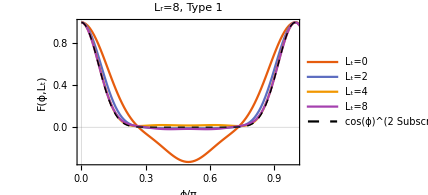

```mathematica
philist=Table[phi,{phi,0,2π,π/100}];
mystyle={FontFamily->"CMU Serif",16,GrayLevel[0]};
figa1=ListLinePlot[{Thread[{philist/π,otocphilist[[;;,2+1,2]]}],Thread[{philist/π,otocphilist[[;;,4+1,2]]}],Thread[{philist/π,otocphilist[[;;,6+1,2]]}],Thread[{philist/π,otocphilist[[;;,Lt+1,2]]}],Thread[{philist/π,Cos[#]^(2*Lr)&/@philist}]},PlotLabel->"L_r="<>ToString[Lr]<>", Type 1",LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->{mystyle,Directive[FontOpacity->0,FontSize->0]},FrameLabel->{HoldForm["ϕ/π"],"F(ϕ,L_t)"},PlotLegends->Placed[LineLegend[Automatic,{"L_t=0","L_t=2","L_t=4","L_t=8","cos(ϕ)^(2 SubscriptBox[L, r])"},Spacings->0.15],{0.6,0.7}],PlotRange->{{0,1.0},All},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Directive[Dashed,Thick,Black]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figa1.pdf"}],figa1]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\fig2a.pdf

# Fig. (b1) Non-Hermitian : OTOC ~ ϕ,L_t

## Run

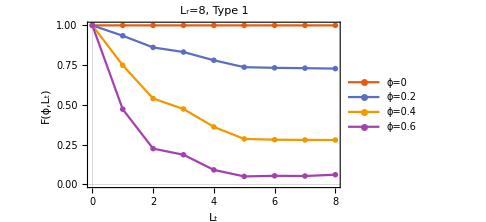

```mathematica
(*Parameter set up
Jz, hz, Jx are system parameters
Lr is the spatial length
Lt is the evolution steps*)
Jz=1.;
hz=0.5;
Jx=1.;
Lr=8;
Lt=8;
(*Parameter ϕ list*)
philist={0,0.2,0.4,0.6};

otocLtlist=(otocType1[Jz,hz,Jx,Lr,Lt,#])&/@philist;
mystyle={FontFamily->"CMU Serif",14,GrayLevel[0]};
figbLtType1=ListLinePlot[Table[Thread[{otocLtlist[[i,;;,1]],otocLtlist[[i,;;,2]]}],{i,1,Length[philist]}],FrameLabel->{HoldForm["L_t"],"F(ϕ,L_t)"},PlotLabel->"L_r="<>ToString[Lr]<>", Type 1",PlotLegends->("ϕ="<>ToString[#]&/@philist),LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,PlotMarkers->"OpenMarkers",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figb1.pdf"}],Show[figbLtType1,ImageSize->{300,200}]]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\fig2b.pdf

# Fig. (c1) Non-Hermitian : (d^2 F)/dϕ^2|_(ϕ=0)

```mathematica
Lrlist={8,9,10};
Jz=1.;
hz=0.5;
Jx=1.;
Lt=8;

dataFcorrd2=(
Lr=#;
Lt=8;
hstep=10^-4;
philist={-hstep,0,hstep};
otocphilist=otocType1[Jz,hz,Jx,Lr,Lt,#]&/@philist;

Fcorrd2=-(otocphilist[[3,;;,2]]-2*otocphilist[[2,;;,2]]+otocphilist[[1,;;,2]])/hstep^2;
Print["L_r=",#];
Thread[{otocphilist[[1,;;,1]],Re[Fcorrd2]}])&/@Lrlist;
```

L_r=8

L_r=9

L_r=10

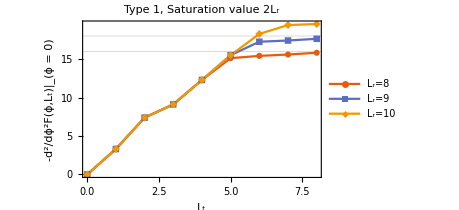

```mathematica
figcFcorrd2Type1=ListLinePlot[dataFcorrd2,PlotMarkers->Automatic,PlotRange->All,LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,FrameLabel->{HoldForm["L_t"],"-d^2/dϕ^2F(ϕ,L_t)|_(ϕ = 0)"},PlotLabel->"Type 1, Saturation value 2L_r",PlotLegends->Placed[LineLegend[Automatic,{"L_r=8","L_r=9","L_r=10"},Spacings->0.15],{0.8,0.2}],GridLines->{{},Table[2*Lr,{Lr,8,10}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figc1.pdf"}],Show[figcFcorrd2Type1,ImageSize->{300,200}]]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\fig2c.pdf

# Fig. (a2) Hermitian: OTOC ~ ϕ,L_t

## Function Definition

```mathematica
(*Dual Parameter*)
Jxtildefunc[Jz_]:=ArcTan[-I*Exp[-2*I*Jz]];
Jztildefunc[Jx_]:=-π/4+I/2*Log[Tan[Jx]];

(*minusAver: When it is true, the function calculate the connected correlator, aka minus the average value.*)
otocType2[Jz_,hz_,Jx_,beta_,Lr_,Lt_,phi_,minusAver_]:=(
H1=N[Sum[pauliOp[i,1,Lr],{i,1,Lr}]//Represent];
(*H2=N[(Sum[pauliOp[i,3,L]·pauliOp[i+1,3,L],{i,1,L-1}]+pauliOp[L,3,L]·pauliOp[1,3,L])//Represent];*)
H2=N[(Sum[pauliOp[i,3,Lr]·pauliOp[i+1,3,Lr],{i,1,Lr}])//Represent];
H3=N[(Sum[pauliOp[i,3,Lr],{i,1,Lr}])//Represent];


(*beta=0.1;*)
Jznew=beta*Jz;
Jxnew=beta*Jx;
hznew=beta*hz;


(*UF=MatrixExp[I*Jxtildefunc[-I*Jz] H1].MatrixExp[I*Jztildefunc[-I*Jx]*H2+hz H3 ];*)
UF=MatrixExp[I*Jxtildefunc[I*Jznew] H1].MatrixExp[I*Jztildefunc[I*Jxnew]*H2-hznew*H3 ];
UFt=IdentityMatrix[(Dimensions[UF])[[1]]];
res={};
a=N[pauliOp[Round[Lr/2],3,Lr]//Represent];

For[i=1,i<Lt+2,i++,

If[minusAver,
rr=Tr[a.UFt.MatrixExp[-I*phi*H3].UFt.a.UFt.MatrixExp[I*phi*H3].UFt]/Tr[UFt.MatrixExp[-I*phi*H3].UFt.UFt.MatrixExp[I*phi*H3].UFt];
rr-=(Tr[UFt.MatrixExp[-I*phi*H3].UFt.a.UFt.MatrixExp[I*phi*H3].UFt]*(Tr[a.UFt.MatrixExp[-I*phi*H3].UFt.UFt.MatrixExp[I*phi*H3].UFt]))/(Tr[UFt.MatrixExp[-I*phi*H3].UFt.UFt.MatrixExp[I*phi*H3].UFt])^2;
,
rr=Tr[a.UFt.MatrixExp[-I*phi*H3].UFt.a.UFt.MatrixExp[I*phi*H3].UFt]/Tr[UFt.MatrixExp[-I*phi*H3].UFt.UFt.MatrixExp[I*phi*H3].UFt];

];

res=Append[res,{i-1,rr}];
(*a=ConjugateTranspose[UF].a.UF;*)
UFt=UFt.UF;
];
res)
```

## Run code

```mathematica
Jz=1.;
hz=0.5;
Jx=1.;
Lr=8;
Lt=8;
beta=0.1;
minusAver=True;

philist=Table[phi,{phi,0,2π,π/100}];
otocphilist=otocType2[Jz,hz,Jx,beta,Lr,Lt,#,minusAver]&/@philist;
```

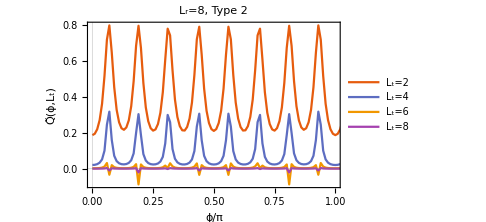

```mathematica
mystyle={FontFamily->"CMU Serif",14,GrayLevel[0]};
figdMinusAverType2=ListLinePlot[{Thread[{philist/π,otocphilist[[;;,2+1,2]]}],Thread[{philist/π,otocphilist[[;;,4+1,2]]}],Thread[{philist/π,otocphilist[[;;,6+1,2]]}],Thread[{philist/π,otocphilist[[;;,Lt+1,2]]}]},LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,FrameLabel->{HoldForm["ϕ/π"],"Q̃(ϕ,L_t)"},PlotLabel->"L_r="<>ToString[Lr]<>", Type 2",PlotLegends->{"L_t=2","L_t=4","L_t=6","L_t=8"},PlotRange->{{0,1.0},All},ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figa2.pdf"}],Show[figdMinusAverType2,ImageSize->{300,200}]]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\fig2d.pdf

# Fig. (b2)

## Run code

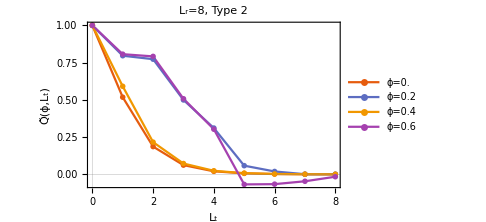

```mathematica
(*philist={0,0.1,0.2,0.4,0.6,0.8,1.0};*)
Jz=1.;
hz=0.5;
Jx=1.;
Lr=8;
Lt=8;

philist={0.,0.2,0.4,0.6};
beta=0.1;

minusAver=True;
otocphilist=otocType2[Jz,hz,Jx,beta,Lr,Lt,#,minusAver]&/@philist;
mystyle={FontFamily->"CMU Serif",14,GrayLevel[0]};
figb2CorrNoMinusAverType2=ListLinePlot[Table[Thread[{otocphilist[[i,;;,1]],otocphilist[[i,;;,2]]}],{i,1,Length[philist]}],LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,FrameLabel->{HoldForm["L_t"],"Q̃(ϕ,L_t)"},PlotLabel->"L_r="<>ToString[Lr]<>", Type 2",PlotLegends->("ϕ="<>ToString[#]&/@philist),PlotRange->All,PlotMarkers->"OpenMarkers",ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figb2.pdf"}],figb2CorrNoMinusAverType2]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\figb2.pdf

# Fig. (c2) Hermitian : (d^2 F)/dϕ^2|_(ϕ=0)

```mathematica
Lrlist={8,9,10};
Jz=1.;
hz=0.5;
Jx=1.;
Lt=8;

dataQcorrd2=(
Lr=#;
Lt=8;
hstep=10^-4;
philist={-hstep,0,hstep};
minusAver=False;
beta=0.1;
otocphilist=otocType2[Jz,hz,Jx,beta,Lr,Lt,#,minusAver]&/@(philist);
Qcorrd2=-1/hstep^2(otocphilist[[3,;;,2]]-2*otocphilist[[2,;;,2]]+otocphilist[[1,;;,2]]);
Thread[{otocphilist[[1,;;,1]],Re[Qcorrd2]}])&/@Lrlist;
```

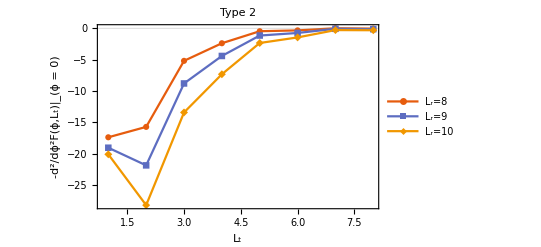

```mathematica
mystyle={FontFamily->"CMU Serif",14,GrayLevel[0]};
figc2=ListLinePlot[dataQcorrd2[[;;,2;;]],PlotMarkers->Automatic,PlotRange->All,LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,FrameLabel->{HoldForm["L_t"],"-d^2/dϕ^2F(ϕ,L_t)|_(ϕ = 0)"},PlotLabel->"Type 2",PlotLegends->{"L_r=8","L_r=9","L_r=10"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs","figc2.pdf"}],figc2]
```

C:\Users\tgzhou\Research\Project\ongoing_project\dual_circuits_otoc\prl_revise\open_source\otoc_dual_skin_effect\figs\figc2.pdf

# Remarks: Program to verify the equivalence via origin and dual system

## Origin

```mathematica
(*Parameter set up
Jz, hz, Jx are system parameters
Lr is the spatial length
Lt is the evolution steps*)
Jz=1.;
hz=0.5;
Jx=1.;
Lr=4;
Lt=3;
(*Parameter ϕ list*)
philist={0,0.1,0.2};

otocLtlistOriginRaw=(otocType1[Jz,hz,Jx,Lr,Lt,#])&/@philist;
mystyle={FontFamily->"CMU Serif",14,GrayLevel[0]};
```

#### Numerical Result Obtained From Origin System

```mathematica
otocLtlistOrigin=otocLtlistOriginRaw[[;;,3;;,2]]//Re
```

{{1.,1.},{0.963663,0.965032},{0.861447,0.868153}}

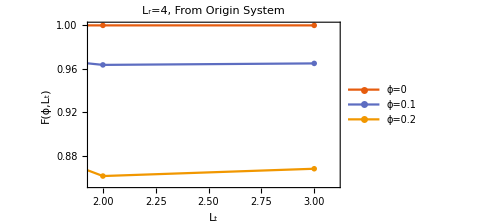

```mathematica
figOrigin=ListLinePlot[Table[Thread[{otocLtlistOriginRaw[[i,;;,1]],otocLtlistOriginRaw[[i,;;,2]]}],{i,1,Length[philist]}],FrameLabel->{HoldForm["L_t"],"F(ϕ,L_t)"},PlotLabel->"L_r="<>ToString[Lr]<>", From Origin System",PlotLegends->("ϕ="<>ToString[#]&/@philist),LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,PlotMarkers->"OpenMarkers",ImageSize->Medium,PlotRange->{{1.95,3.1},{All,All}}]
```

## Dual: Eq. (9) in the main text

## Only works L_t>1

```mathematica
Jxtildefunc[Jz_]:=ArcTan[-I*Exp[-2*I*Jz]];
Jztildefunc[Jx_]:=-(π/4)+(I/2)*Log[Tan[Jx]];

otocfuncDual[Jz_,hz_,Jx_,phi_,Lt_,Lr_]:=(

opMsystem1=N[(pauliOp[Lt+1,3,4*Lt]//Represent)];
opMsystem2=N[(pauliOp[3*Lt+1,3,4*Lt]//Represent)];
Clear[j];
If[Lt≠ 1,
H1=Table[N[Sum[pauliOp[i+j*Lt,1,4*Lt],{i,2,Lt}]//Represent],{j,0,3}];
H2=Table[N[(Sum[pauliOp[i+j*Lt,3,4*Lt]·pauliOp[i+j*Lt+1,3,4*Lt],{i,1,Lt}])//Represent],{j,0,3}];
H3=Table[N[(Sum[pauliOp[i+j*Lt,3,4*Lt],{i,2,Lt}])//Represent],{j,0,3}];
,
H1=Table[N[pauliOp[i+j*Lt,1,4*Lt]//Represent]*0.,{j,0,3}];
H2=Table[N[(Sum[pauliOp[i+j*Lt,3,4*Lt]·pauliOp[i+j*Lt+1,3,4*Lt],{i,1,Lt}])//Represent],{j,0,3}];
H1=Table[N[pauliOp[i+j*Lt,1,4*Lt]//Represent]*0.,{j,0,3}];];
coefflistH1=I*{Jxtildefunc[Jz],Jxtildefunc[-Jz],Jxtildefunc[Jz],Jxtildefunc[-Jz]};
coefflistH2=I*{Jztildefunc[Jx],Jztildefunc[-Jx],Jztildefunc[Jx],Jztildefunc[-Jx]};
coefflistH3=I*{hz,-hz,hz,-hz};
(*coefflistH1=I*{Jxtilde,-Conjugate[Jxtilde],Jxtilde,-Conjugate[Jxtilde]};
coefflistH2=I*{Jztilde,-Conjugate[Jztilde],Jxtilde,-Conjugate[Jztilde]};
coefflistH3=I*{hz,-hz,hz,-hz};*)
(*Print[phi];*)

U=MatrixExp[Sum[H1[[k]]*coefflistH1[[k]],{k,1,4}]].MatrixExp[Sum[H2[[k]]*coefflistH2[[k]],{k,1,4}]+Sum[H3[[k]]*coefflistH3[[k]],{k,1,4}]-I*phi*opMsystem1+I*phi*opMsystem2];


opbound1=N[((pauliOp[1,0,4*Lt]+pauliOp[1,1,4*Lt])//Represent)];
opbound2=N[((pauliOp[Lt+1,0,4*Lt]+pauliOp[Lt+1,1,4*Lt])//Represent)];
opbound3=N[((pauliOp[2*Lt+1,0,4*Lt]+pauliOp[2*Lt+1,1,4*Lt])//Represent)];
opbound4=N[((pauliOp[3*Lt+1,0,4*Lt]+pauliOp[3*Lt+1,1,4*Lt])//Represent)];

opSz1=N[(pauliOp[1,3,4*Lt]//Represent)];
opSz2=N[(pauliOp[Lt*2+1,3,4*Lt]//Represent)];
ULr=MatrixPower[(opbound1).opbound2.opbound3.opbound4.U,Lr];
(*Tr[ULr]*)
otoc=Re[Tr[ULr.(opSz1).opSz2]/Tr[ULr]]
)
```

```mathematica
(*Parameter set up
Jz, hz, Jx are system parameters
Lr is the spatial length
Lt is the evolution steps*)
Jz=1.;
hz=0.5;
Jx=1.;
Lr=4;
Lt=3;
Ltlist=Table[i,{i,2,Lt}];
philist={0.0,0.1,0.2};

otocLtlistDual=(Table[Print["L_t=",i," ϕ=",#];otocfuncDual[Jz,hz,Jx,#,i,Lr],{i,2,Lt}])&/@philist
```

L_t=2 ϕ=0.

L_t=3 ϕ=0.

L_t=2 ϕ=0.1

L_t=3 ϕ=0.1

L_t=2 ϕ=0.2

L_t=3 ϕ=0.2

### Numerical Result Obtained From Dual System

```mathematica
otocLtlistDual={{1.0000000000000002,1.0000000000000002},{0.9636631396979058,0.9650319317392441},{0.8614469701471346,0.8681528843626677}}
```

{{1.,1.},{0.963663,0.965032},{0.861447,0.868153}}

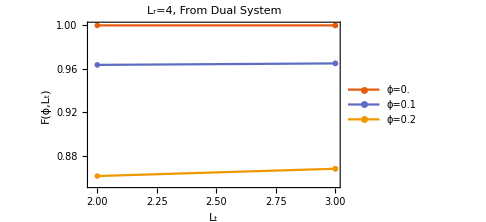

```mathematica
figDual=ListLinePlot[Table[Thread[{Ltlist,otocLtlistDual[[i,;;]]}],{i,1,Length[philist]}],FrameLabel->{HoldForm["L_t"],"F(ϕ,L_t)"},PlotLabel->"L_r="<>ToString[Lr]<>", From Dual System",PlotLegends->("ϕ="<>ToString[#]&/@philist),LabelStyle->mystyle,FrameStyle->mystyle,FrameTicksStyle->mystyle,PlotMarkers->"OpenMarkers",ImageSize->Medium]
```

## Numerical Verification

```mathematica
otocLtlistOrigin==otocLtlistDual
```

True